# :d83d:dcab Bset 2: All Pendulums. All the time.

```mathematica
SetDirectory@NotebookDirectory[];
<<"../MMA library.m"
```

## Planar Pendulum

```mathematica
With[{context="s1`"},If[Context[] ≠ context,Begin[context]]];Dynamic[Refresh[Context[],UpdateInterval->1]]
```

### Step 2: Define reasonable constants

```mathematica
parameters={m->1,l->1,g->QuantityMagnitude@UnitConvert@Entity["Planet","Earth"]["Gravity"]}
```

{m→1,l→1,g→9.8}

### Step 1: Define FBDs

### Step 2: Define vector force equations

```mathematica
ClearAll[θ,fn,fg];
θ[t_]:=ArcTan[y[t],x[t]];
fn=tension[t]*{-Sin[θ[t]],Cos[θ[t]]};
fg=m g {0,-1};
```

### Step 3: Determine equations of motion

```mathematica
eq1=fn+fg==m {x''[t],y''[t]}
```

{-(tension[t] x[t])/(√(x[t]^2+y[t]^2)),-g m+(tension[t] y[t])/(√(x[t]^2+y[t]^2))}=={m x''[t],m y''[t]}

```mathematica
constraint=Norm@{x[t],y[t]}==l
```

√(Abs[x[t]]^2+Abs[y[t]]^2)==l

### Cylindrical equations

```mathematica
ClearAll[r,θ]
eqr=tension[t]-m g Sin[θ[t]]==(r''[t]-r [t]θ'[t])m
eqθ=-m g Sin[θ[t]]==m(2 r'[t] θ'[t]+r[t] θ''[t])
```

-g m Sin[θ[t]]+tension[t]==m (-r[t] θ'[t]+r''[t])

-g m Sin[θ[t]]==m (2 r'[t] θ'[t]+r[t] θ''[t])

```mathematica
Module[{r=r,θ=θ},
r[t_]:=l;
θ[t_]:=ArcTan[y[t],x[t]];
FullSimplify@Solve[{eqr,eqθ},{x''[t],y''[t]}]]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{y''[t]→(tension[t] (x[t]^2+y[t]^2)^2+m (y[t] x'[t]-x[t] y'[t]) (r x[t]^2-2 l x[t] x'[t]+y[t] (r y[t]-2 l y'[t]))+l m y[t] (x[t]^2+y[t]^2) x''[t])/(l m x[t] (x[t]^2+y[t]^2))}}

### Run Simulation

```mathematica
ClearAll[r]
constraint=r[t]==l
```

```mathematica
initialConditions={θ[0]==0,θ'[0]==2}
```

{θ[0]==0,θ'[0]==2}

```mathematica
sol=NDSolveValue[{eqr,eqθ,constraint,initialConditions}/.parameters,{r[t],tension[t],θ[t]},{t,0,10}];
```

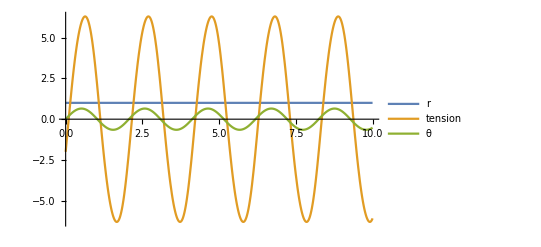

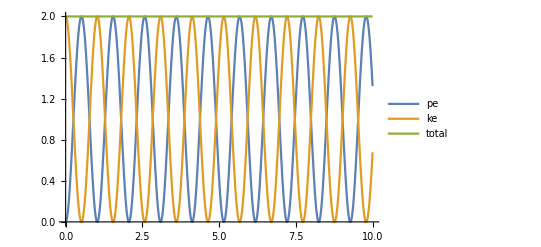

```mathematica
pe[t_]:=(-m g Cos[sol[[3,0]][t]]+m g l) /. parameters;
ke[t_]:=1/2 m (sol[[1,0]][t] sol[[3,0]]'[t])^2/.parameters;
Plot[Evaluate@sol,{t,0,10},PlotRange->Full,PlotLegends->StringSplit@"r tension θ"]
Plot[Evaluate@{pe[t],ke[t], pe[t]+ke[t]},{t,0,10},PlotLegends->StringSplit@"pe ke total"]
```

### Add viscous drag

```mathematica
ClearAll[r,θ]
eqr=tension[t]-m g Sin[θ[t]]==(r''[t]-r [t]θ'[t])m
eqθ=-m g Sin[θ[t]]-.1 θ'[t]==m(2 r'[t] θ'[t]+r[t] θ''[t])
```

-g m Sin[θ[t]]+tension[t]==m (-r[t] θ'[t]+r''[t])

-g m Sin[θ[t]]-0.1 θ'[t]==m (2 r'[t] θ'[t]+r[t] θ''[t])

```mathematica
sol=NDSolveValue[{eqr,eqθ,constraint,initialConditions}/.parameters,{r[t],tension[t],θ[t]},{t,0,10}];
```

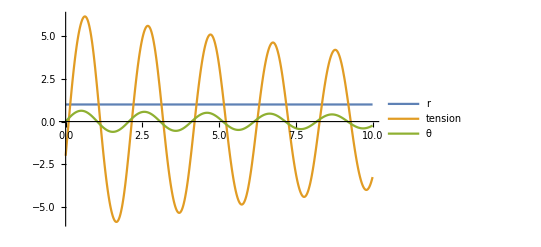

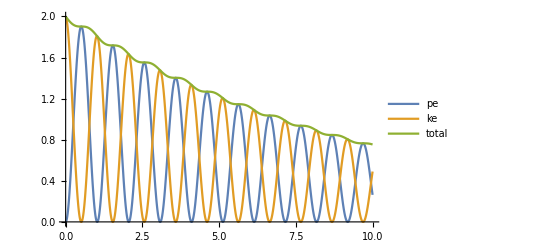

```mathematica
pe[t_]:=(-m g Cos[sol[[3,0]][t]]+m g l) /. parameters;
ke[t_]:=1/2 m (sol[[1,0]][t] sol[[3,0]]'[t])^2/.parameters;
Plot[Evaluate@sol,{t,0,10},PlotRange->Full,PlotLegends->StringSplit@"r tension θ"]
Plot[Evaluate@{pe[t],ke[t], pe[t]+ke[t]},{t,0,10},PlotLegends->StringSplit@"pe ke total"]
```

### Add air drag

```mathematica
ClearAll[r,θ]
eqr=tension[t]-m g Sin[θ[t]]==(r''[t]-r [t]θ'[t])m
eqθ=-m g Sin[θ[t]]-.1Abs[θ'[t]]^2 Sign[ θ'[t]]==m(2 r'[t] θ'[t]+r[t] θ''[t])
```

-g m Sin[θ[t]]+tension[t]==m (-r[t] θ'[t]+r''[t])

-g m Sin[θ[t]]-0.1 Sign[θ'[t]] θ'[t]^2==m (2 r'[t] θ'[t]+r[t] θ''[t])

```mathematica
sol=NDSolveValue[{eqr,eqθ,constraint,initialConditions}/.parameters,{r[t],tension[t],θ[t]},{t,0,10},Method->{"IndexReduction"->Automatic}];
```

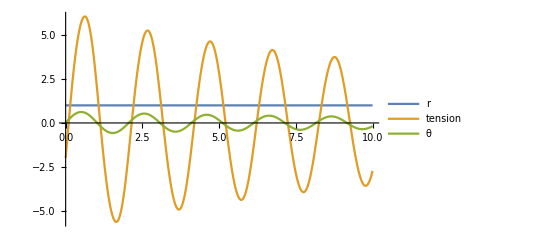

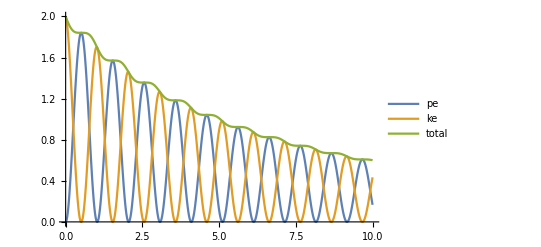

```mathematica
pe[t_]:=(-m g Cos[sol[[3,0]][t]]+m g l) /. parameters;
ke[t_]:=1/2 m (sol[[1,0]][t] sol[[3,0]]'[t])^2/.parameters;
Plot[Evaluate@sol,{t,0,10},PlotRange->Full,PlotLegends->StringSplit@"r tension θ"]
Plot[Evaluate@{pe[t],ke[t], pe[t]+ke[t]},{t,0,10},PlotLegends->StringSplit@"pe ke total",PlotRange->Full]
```

### Cleanup

```mathematica
With[{context="s1`"},If[Context[]==context,End[]]];Dynamic[Refresh[Context[],UpdateInterval->1]]
```

## Springy Pendulum

```mathematica
With[{context="s2`"},If[Context[] ≠ context,Begin[context]]];Dynamic[Refresh[Context[],UpdateInterval->1]]
```

### Define reasonable constants

```mathematica
parameters={m->1,l->1,g->QuantityMagnitude@UnitConvert@Entity["Planet","Earth"]["Gravity"],k->6}
```

{m→1,l→1,g→9.8,k→6}

### Setup equations of motion

```mathematica
ClearAll[r,θ,t]
eqr=-k(r[t]-l)+m g Cos[θ[t]]==m(r''[t]-r [t]θ'[t])
eqθ=-m g Sin[θ[t]]==m(2 r'[t] θ'[t]+r[t] θ''[t])
```

g m Cos[θ[t]]-k (-l+r[t])==m (-r[t] θ'[t]+r''[t])

-g m Sin[θ[t]]==m (2 r'[t] θ'[t]+r[t] θ''[t])

### Run Simulation

```mathematica
timerange={t,0,.5};
```

```mathematica
initialConditions={r[0]==l,r'[0]==0,θ[0]==-1,θ'[0]==0}
```

{r[0]==l,r'[0]==0,θ[0]==-1,θ'[0]==0}

```mathematica
sol=NDSolveValue[{eqr,eqθ,initialConditions}/.parameters,{r[t],θ[t]},{t,0,10}];
```

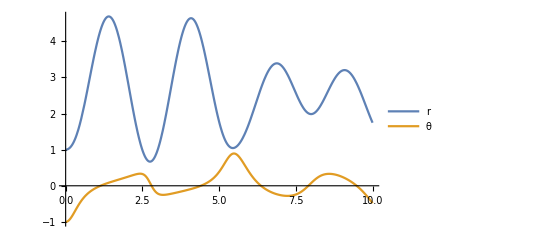

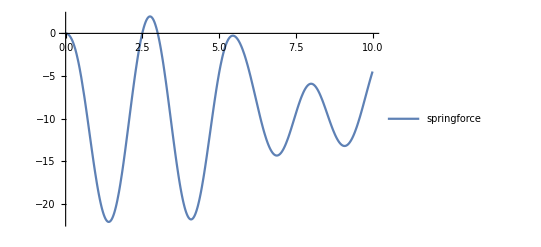

```mathematica
pe[t_]:=(-m g Cos[sol[[2,0]][t]]+m g l) /. parameters;
ke[t_]:=1/2 m (sol[[1,0]][t] sol[[3,0]]'[t])^2/.parameters;
springforce[t_]:=-k(sol[[1,0]][t]-l)/.parameters
Plot[Evaluate@sol,{t,0,10},PlotRange->Full,PlotLegends->StringSplit@"r θ"]
Plot[Evaluate@{springforce[t]},{t,0,10},PlotLegends->StringSplit@"springforce"]
(*Plot[Evaluate@{pe[t],ke[t], pe[t]+ke[t]},{t,0,2},PlotLegends->StringSplit@"pe ke total"]*)
```

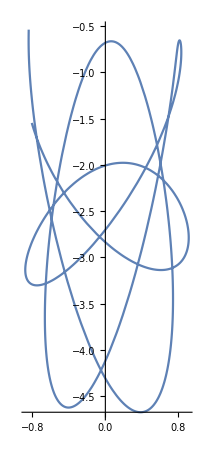

~/Pictures/plot.png

```mathematica
ParametricPlot[RotationMatrix[sol[[2]]].{0,-sol[[1]]},{t,0,10},AspectRatio->Automatic]
Export["~/Pictures/plot.png",%]
```

### Cleanup

```mathematica
With[{context="s2`"},If[Context[]==context,End[]]];Dynamic[Refresh[Context[],UpdateInterval->1]]
```

## Spinny pendulum

```mathematica
With[{context="s3`"},If[Context[] ≠ context,Begin[context]]];Dynamic[Refresh[Context[],UpdateInterval->1]]
```

### Define reasonable constants

```mathematica
parameters={m->1,l->1,g->QuantityMagnitude@UnitConvert@Entity["Planet","Earth"]["Gravity"],k->100,Ω->30}
```

{m→1,l→1,g→9.8,k→100,Ω→30}

### Setup equations of motion

```mathematica
ClearAll[r,θ1,t]
fg = m g;
ft=k(r[t]-l);
fc=m Ω r[t] Sin[θ[t]];
eqr=-ft+fg Cos[θ[t]]+fc Sin[θ[t]]==m(r''[t]-r [t]θ'[t])
eqθ=-fg Sin[θ[t]]+fc Cos[θ[t]]==m(2 r'[t] θ'[t]+r[t] θ''[t])
```

g m Cos[θ[t]]-k (-l+r[t])+m Ω r[t] Sin[θ[t]]^2==m (-r[t] θ'[t]+r''[t])

-g m Sin[θ[t]]+m Ω Cos[θ[t]] r[t] Sin[θ[t]]==m (2 r'[t] θ'[t]+r[t] θ''[t])

### Run Simulation

```mathematica
initialConditions={r[0]==l,r'[0]==0,θ[0]==.1,θ'[0]==0}
```

{r[0]==l,r'[0]==0,θ[0]==0.1,θ'[0]==0}

```mathematica
sol=NDSolveValue[{eqr,eqθ,initialConditions}/.parameters,{r[t],θ[t]},{t,0,10}];
```

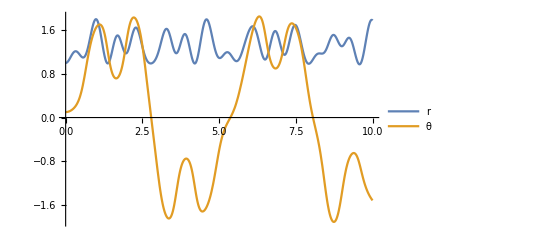

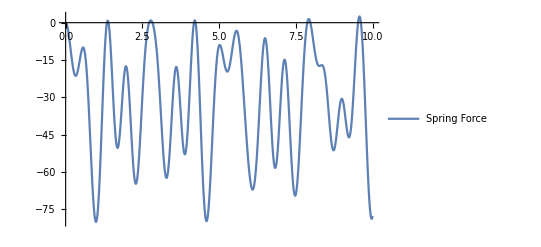

```mathematica
pe[t_]:=(-m g Cos[sol[[2,0]][t]]+m g l) /. parameters;
ke[t_]:=1/2 m (sol[[1,0]][t] sol[[3,0]]'[t])^2/.parameters;
springforce[t_]:=-k(sol[[1,0]][t]-l)/.parameters
Plot[Evaluate@sol,{t,0,10},PlotRange->Full,PlotLegends->StringSplit@"r θ"]
Plot[Evaluate@{springforce[t]},{t,0,10},PlotLegends->StringSplit["Spring Force",","]]
```

-Graphics3D-

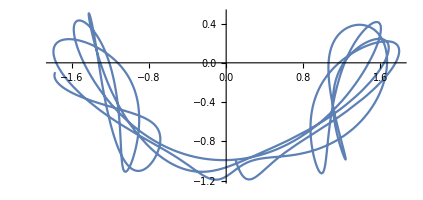

```mathematica
ParametricPlot3D[RotationMatrix[Ω t/.parameters,{0,1,0}].RotationMatrix[sol[[2]],{0,0,1}].{0,-sol[[1]],0},{t,0,10},AspectRatio->Automatic]

ParametricPlot[RotationMatrix[sol[[2]]].{0,-sol[[1]]},{t,0,10},AspectRatio->Automatic]
```

### Cleanup

```mathematica
With[{context="s3`"},If[Context[]==context,End[]]];Dynamic[Refresh[Context[],UpdateInterval->1]]
```

## Scratch Work

```mathematica
exportNotebookPDF[]
```

/home/eric/Documents/School/QEA2/Attitude/Bset 2/Mathematica work.pdf